# 4.2 Renyi dimension of weighted Cantor set

#### b)

As derived analytically in question a), the Renyi dimension Dq is given by:

```mathematica
Dq = 1/(1-q)*Log[(1/3)^q+(2/3)^q]/Log[3]
```

Log[(2/3)^q+3^-q]/((1-q) Log[3])

```mathematica
p1 = Plot[Dq,{q,-20,20}, AxesLabel->{"q", "D_q"}];
```

```mathematica
p2 = Plot[1, {q,-20,20}, PlotStyle->{Red,Dashed}, PlotLegends->{"D_(-∞)"}];
```

```mathematica
p3= Plot[Log[3/2]/Log[3], {q,-20,20}, PlotStyle->{Blue,Dashed}, PlotLegends->{"D_(+∞)"}];
```

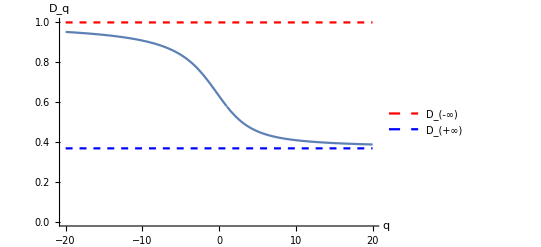

```mathematica
Show[p1,p2,p3, PlotRange->{{-20,20}, {0,1}}, AxesOrigin->Automatic]
```

One can clearly see that D_q is a non-increasing function of q which converges to D_(-∞) (resp. D_(+∞)) in the limit q to -∞ (resp. +∞).

#### c)

```mathematica
D2 = Dq/. q-> 2
```

Log[9/5]/Log[3]

```mathematica
N[Log[9/5]/Log[3]]
```

0.535026

```mathematica
D1 = Limit[Dq,q->1]
```

Log[27/4]/Log[27]

```mathematica
N[Log[27/4]/Log[27]]
```

0.57938

So the information dimension D1 equals Log[27/4]/Log[27]≈0.57938, while the correlation dimension D2 turns out to be Log[9/5]/Log[3]≈0.535026. Note that indeed D1 > D2.

#### d)

```mathematica
Dinf = Limit[Dq,q->∞] (* D∞ *)
```

Log[3/2]/Log[3]

```mathematica
N[Log[3/2]/Log[3]]
```

0.36907

```mathematica
Dminf = Limit[Dq,q->-∞] (* D-∞ *)
```

1

So the limit D∞ equals Log[3/2]/Log[3] ≈ 0.36907, while D-∞ turns out to be 1. Note that indeed D-∞>D1>D2>D∞.